```mathematica
(*This will be a notebook containing all the date/plots to for Kaden.*)


(*First, get data for the 1D well*)
```

```mathematica
(*Box length must be bigger than 2*b (interwell seperation), and it also must be bigger than b+4. And, because for the 2D case we can only comfortably work with 25-30 basis states, our resolution is limited to L/30. Assume we will work with a max interwell of 4(results start getting crappy around 4-6), this gives us a L of 8-9. I will make it 9, and we have a maximum resolution of about .3)
```

```mathematica
TunnelingInterwellP1D=Table[{p,Log[computePlaneMatrix2Well[10,.5,p/2,9,30][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,9,30][[1]][[1]]]},{p,0,4,.1}];
```

```mathematica
TunnelingInterwell2D = Table[{b,Log[Tunneling2D[10,9,30,b]]},{b,0,4,.2}]
```

{{0.,1.9044},{0.2,1.87605},{0.4,1.78933},{0.6,1.63913},{0.8,1.41653},{1.,1.1089},{1.2,0.702326},{1.4,0.190366},{1.6,-0.411329},{1.8,-1.06492},{2.,-1.73476},{2.2,-2.40311},{2.4,-3.06517},{2.6,-3.72117},{2.8,-4.37314},{3.,-5.02162},{3.2,-5.66683},{3.4,-6.31323},{3.6,-6.95727},{3.8,-7.60098},{4.,-8.28419}}

```mathematica
(*There seems to be weird behaviour at around b=4*)
```

```mathematica
p1 = ListPlot[TunnelingInterwellP1D,AxesLabel->{"interwell sep (sp. sz)","τ"}]
```

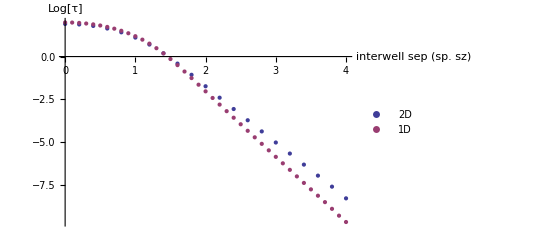

```mathematica
p2 = ListPlot[{TunnelingInterwell2D,TunnelingInterwellP1D},AxesLabel->{"interwell sep (sp. sz)","Log[τ]"},PlotLegends->{"2D","1D"}]
```

```mathematica
(*Show what happens as the depth is varied*)
```

```mathematica
TunnelingInterwell2DVaryV= Table[{b,Log[Tunneling2D[b,9,30,1]]},{b,5,20,.5}]
```

{{5.,0.70175},{5.5,0.764884},{6.,0.819999},{6.5,0.86886},{7.,0.912711},{7.5,0.952458},{8.,0.988783},{8.5,1.02222},{9.,1.05317},{9.5,1.08197},{10.,1.1089},{10.5,1.13418},{11.,1.15799},{11.5,1.18049},{12.,1.20181},{12.5,1.22206},{13.,1.24135},{13.5,1.25976},{14.,1.27736},{14.5,1.29422},{15.,1.3104},{15.5,1.32595},{16.,1.34092},{16.5,1.35534},{17.,1.36926},{17.5,1.3827},{18.,1.3957},{18.5,1.40829},{19.,1.42048},{19.5,1.43231},{20.,1.44379}}

```mathematica
TunnelingInterwellP1DVaryV=Table[{p,Log[computePlaneMatrix2Well[p,.5,.5,9,30][[1]][[2]]-computePlaneMatrix2Well[p,.5,.5,9,30][[1]][[1]]]},{p,5,20,.1}];
```

```mathematica
TunnelingInterwellP1D[[11]]
```

{1.,1.18983}

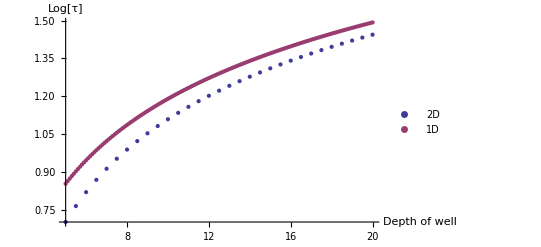

```mathematica
ListPlot[{TunnelingInterwell2DVaryV,TunnelingInterwellP1DVaryV},AxesLabel->{"Depth of well","Log[τ]"},PlotLegends->{"2D","1D"}]
```

```mathematica
Manipulate[ListPlot[Table[{p,Log[computePlaneMatrix2Well[p,.5,b,9,20][[1]][[2]]-computePlaneMatrix2Well[p,.5,b,9,20][[1]][[1]]]},{p,5,20,1}]],{b,0,3,.1}]
```

Part::partd: Part specification 5 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 5 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 6 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification 5 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 5 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 6 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
(*Make a plot that shows this. As the depth gets bigger, I would expect all the values to approach each other*)
TunnelingVaryVVaryB = Table[{b/2.,Table[{V,Log[computePlaneMatrix2Well[V,.5,b/2.,12,200][[1]][[2]]-computePlaneMatrix2Well[V,.5,b/2.,12,200][[1]][[1]]]},{V,5,100,3}]},{b,{0,1,2,4,6}}];
```

```mathematica
Table[{p,computePlaneMatrix2Well[p,.5,.5,9,70][[1]][[2]]-computePlaneMatrix2Well[p,.5,.5,9,70][[1]][[1]]},{p,5,20,2}]
```

{{5,2.34764},{7,2.77935},{9,3.13097},{11,3.43165},{13,3.69657},{15,3.93475},{17,4.15207},{19,4.35255}}

```mathematica
TunnelingVaryVVaryB[[4]]
```

{2.,{{5,-6.26116},{8,-8.40093},{11,-10.2495},{14,-11.9},{17,-13.4053},{20,-14.7984},{23,-16.1021},{26,-17.3365},{29,-18.5405},{32,-19.9377},{35,-21.0021},{38,-19.6512},{41,-18.9697},{44,-18.4226},{47,-17.9223},{50,-17.4665},{53,-17.038},{56,-16.6392},{59,-16.2631},{62,-15.9081},{65,-15.5737},{68,-15.2563},{71,-14.955},{74,-14.6687},{77,-14.3956},{80,-14.1352},{83,-13.8862},{86,-13.6478},{89,-13.4193},{92,-13.2},{95,-12.9892},{98,-12.7865}}}

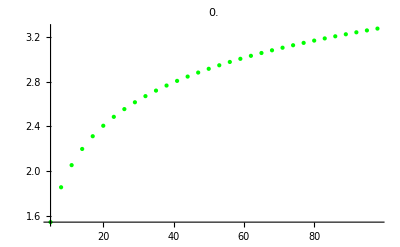
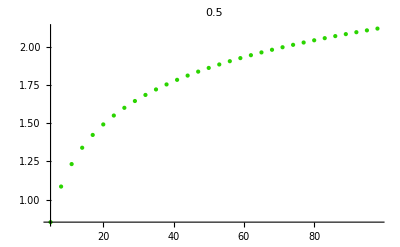
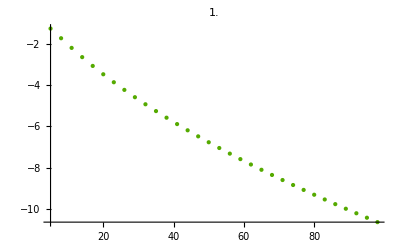
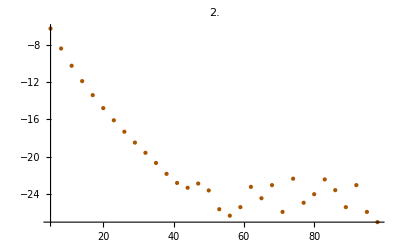
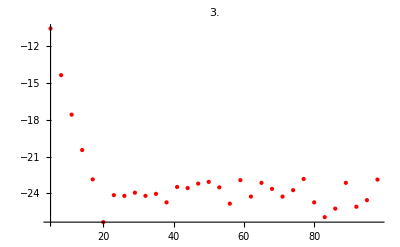

```mathematica
PlotListVVaryB=ListPlot[#[[2]],PlotLabel->#[[1]],PlotRange->All,PlotStyle->RGBColor[#1[[1]]/3.,(3-#1[[1]])/3,0]]&/@TunnelingVaryVVaryB
```

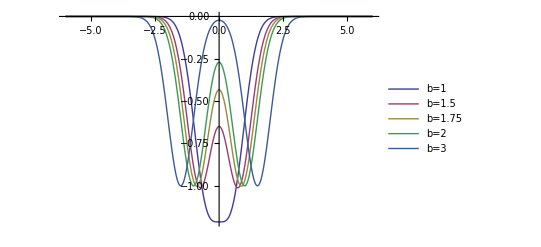

```mathematica
Plot[Evaluate[Table[-1*Exp[-2.*(x-b/2.)^2.]-1*Exp[-2.*(x+b/2.)^2.],{b,{1,1.5,1.75,2,3}}]],{x,-6,6},PlotLegends->{"b=1","b=1.5","b=1.75","b=2","b=3"}]
```

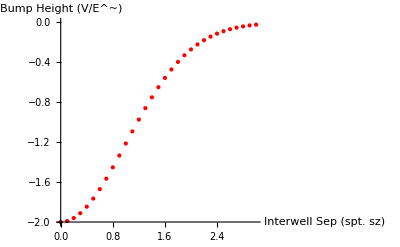

```mathematica
ListPlot[Table[{b,-1*Exp[-2.*(0-b/2.)^2.]-1*Exp[-2.*(0+b/2.)^2.]},{b,0,3,.1}],PlotStyle->Red,AxesLabel->{"Interwell Sep (spt. sz)","Bump Height (V/E^~)"}]
```

```mathematica
Manipulate[Plot[-V*Exp[-2.*(x-b/2.)^2.]-V*Exp[-2.*(x+b/2.)^2.],{x,-12,12},PlotRange->All],{V,0,100},{b,0,3}]
```

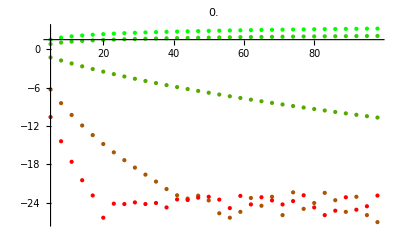

```mathematica
Show[PlotListVVaryB]
```

```mathematica
TunnelingVaryVVaryBver2 = Table[{b,Table[{V,Log[computePlaneMatrix2Well[V,.5,b/2.,10,200][[1]][[2]]-computePlaneMatrix2Well[V,.5,b/2.,10,200][[1]][[1]]]},{V,5,700,10}]},{b,{1,1.5,1.75,2,3}}];
```

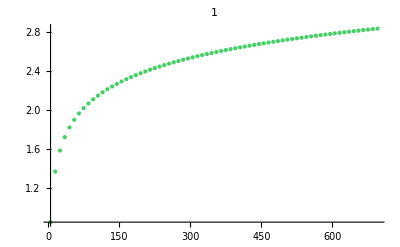
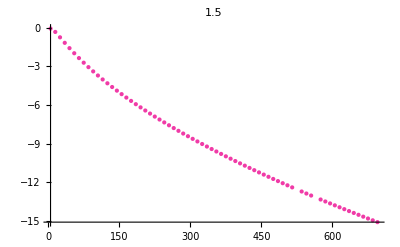
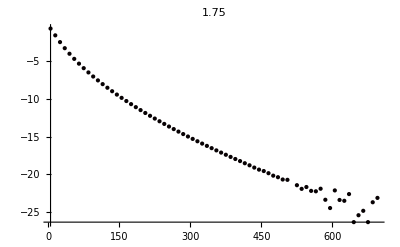
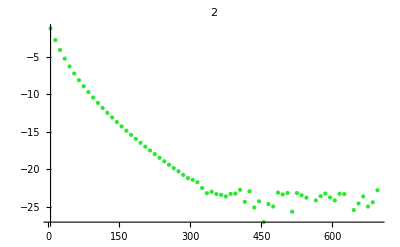
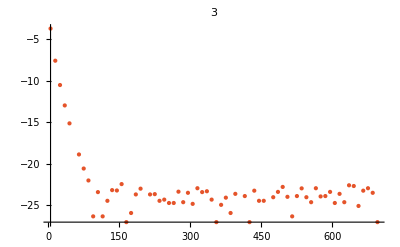

```mathematica
PlotListVVaryBver2=ListPlot[#[[2]],PlotLabel->#[[1]],PlotRange->All,PlotStyle->RGBColor[RandomReal[],RandomReal[],RandomReal[]]]&/@TunnelingVaryVVaryBver2
```

```mathematica
t1 = Transpose[TunnelingVaryVVaryBver2];
```

```mathematica
t1[[1]]
```

```mathematica
Export["tunnelingVandb.pdf",ListPlot[t1[[2]], PlotLegends->{t1[[1]]},AxesLabel->{"Log[V/E~]","Log[J/E^~]"}]]
```

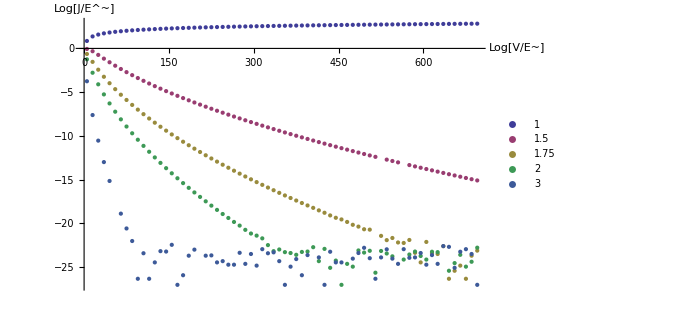

```mathematica
ListPlot[t1[[2]], PlotLegends->{t1[[1]]},AxesLabel->{"Log[V/E~]","Log[J/E^~]"}]
```

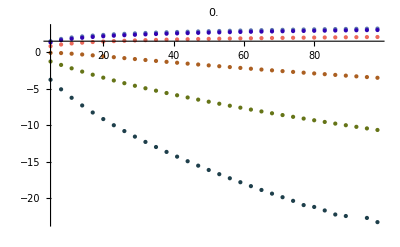

```mathematica
Show[PlotListVVaryBver2]
```

```mathematica
(*Testing adam's results*)
tun = (computePlaneMatrix2Well[Vkauf,.5,bkauf/2.,12,10][[1]][[2]]-computePlaneMatrix2Well[Vkauf,.5,bkauf/2.,12,10][[1]][[1]])
```

313.303

```mathematica
H=computePlaneMatrix2WellH[Vkauf,.5,bkauf/2.,12,10];
```

```mathematica
Im[H[[3]][[4]]]
```

0.

```mathematica
H[[1]][[1]]
```

-316.424+0. ⅈ

```mathematica
Fme[x_,k_,w_,V_,b_] = Integrate[-Exp[-ⅈ(k-w)*x]V*(Exp[-2*(x-b)^2]+Exp[-2*(x-b)^2]),{x,-∞,∞}]
```

-ⅇ^(-1/8 (k-w) (8 ⅈ b+k-w)) √(2 π) V

```mathematica
Fme[x_,k_,w_,V_,b_] = Integrate[-Exp[-ⅈ(k-w)*x]V*(Exp[-2*(x-b)^2]+Exp[-2*(x-b)^2]),{x,-∞,∞}]
```

```mathematica
computePlaneMatrix2Well[10,.5,1.2/2.,12,40][[1]][[2]]
```

-10006.5

```mathematica
computePlaneMatrix2Well[Vkauf,.5,bkauf/2.,12,40][[1]][[1]]
```

-11815.4

```mathematica
0.336255042011544
```

```mathematica
0.336255042011544*206.7566758825286/2
```

34.7615

```mathematica
%*206.76136213516995/2
```

32389.5

```mathematica
0.336255042011544*206.76/2
```

34.762

```mathematica
67.42958868180881
```

134.859

```mathematica
1.18/2
```

0.59

```mathematica
0.3264722992789757*206.54
```

67.4296

```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Convert[PlanckConstantReduced^2/(86.909 AtomicMassUnit*(750 Nano Meter)^2*PlanckConstant),Hertz]
```

206.757 Hertz

```mathematica
Vkauf=3162.5868653672755*100/scalin
```

1529.58

```mathematica
bkauf=.9/.75
```

1.2

```mathematica
PlanckConstant
```

6.62607×10^-34 Joule Second

```mathematica
2*π*PlanckConstantReduced
```

6.62607×10^-34 Joule Second

```mathematica
Convert[87 AtomicMassUnit,Kilogram]
```

1.44467×10^-25 Kilogram

```mathematica
Integrate[Cos[(l-m)*x]*Exp[-2*(x-bsep)^2/□
```

```mathematica
computePlaneMatrix2WellBox
```

```mathematica
(*Testing adam's results*)
tun = (computePlaneMatrix2WellBox[Vkauf,.5,bkauf/2.,12,100][[1]][[2]]-computePlaneMatrix2WellBox[Vkauf,.5,bkauf/2.,12,100][[1]][[1]])
```

19.2357

### Looking at Adam’s Code: Finding the difference

```mathematica
scalin = 206.76136213516995
```

206.761

```mathematica
Fme[k_,w_,V_,b_] = Integrate[-Exp[-ⅈ(k-w)*x]V*(Exp[-2*(x-b)^2]+Exp[-2*(x+b)^2]),{x,-∞,∞}]
```

-ⅇ^(-1/8 (k-w) (8 ⅈ b+k-w)) (1+ⅇ^(2 ⅈ b (k-w))) √(π/2) V

```mathematica
Fmeinf[k_,w_,V_,b_,L_] = Integrate[-Exp[-ⅈ(k-w)*x]V*(Exp[-2*(x-b)^2]+Exp[-2*(x+b)^2]),{x,-L/2,L/2}]
```

1/2 ⅇ^(-1/8 (k-w) (8 ⅈ b+k-w)) √(π/2) V (ⅇ^(2 ⅈ b (k-w)) (Erf[(4 b-2 L+ⅈ (k-w))/(2 √2)]-Erf[(4 b+2 L+ⅈ (k-w))/(2 √2)])+Erf[(4 b-ⅈ k-2 L+ⅈ w)/(2 √2)]-Erf[(4 b-ⅈ k+2 L+ⅈ w)/(2 √2)])

```mathematica
Fhim[k_,w_,V_,b_] = Integrate[-Cos[-ⅈ(k-w)x]V*(Exp[-2*(x-b)^2]+Exp[-2*(x+b)^2]),{x,-∞,∞}]
```

-ⅇ^(-2 b^2) (ⅇ^(1/8 (4 b+k-w)^2)+ⅇ^(1/8 (4 b-k+w)^2)) √(π/2) V

```mathematica
Fhim2[k_,w_,V_,b_]=Integrate[(-(Exp[-ⅈ(k-w)x]+Exp[ⅈ(k-w)x]))/2 V*(Exp[-2*(x-b)^2]+Exp[-2*(x+b)^2]),{x,-∞,∞}]
```

-ⅇ^(-2 b^2) (ⅇ^(1/8 (4 b-ⅈ (k-w))^2)+ⅇ^(1/8 (4 b+ⅈ (k-w))^2)) √(π/2) V

```mathematica
H=computePlaneMatrix2WellH[Vkauf,.5,bkauf/2.,12,99];
```

```mathematica
(*HamK[[1]][[1]]/(2*π*ℏ)=708.5600172585082
 for L = 12, # basis = 11 for his values E0 = 100, b = .9*)
```

```mathematica
Fme[1,1,Vkauf,bkauf]
```

-3838.21+0. ⅈ

```mathematica
(H[[1]][[1]]+Fderv[1,1,bkauf/2.,.5,12,Vkauf])*scalin
```

69446.+0. ⅈ

```mathematica
(*Calculate the actual value m^2/2 (note, h11 starts at -p/2)
```

```mathematica
((2*(π*()/12))^2/2//N
```

3.42695

```mathematica
%scalin
```

42750.3

```mathematica
(2*(π*(102/2-1))/12)^2/2*scalin//N
```

70856.

```mathematica
(*So it matches up. So I can isolate the behaviour, in the off diagonals*)
```

```mathematica
Fderv[l_,m_,b_,c_,length_,V_]:=V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length
```

```mathematica
Fme[2,2,1,bkauf/2]
```

-2.50663+0. ⅈ

```mathematica
Fderv[2,2,bkauf/2,.5,1,1]
```

2.50663+0. ⅈ

```mathematica
Fhim[2,2,1,bkauf/2]
```

-2.50663

```mathematica
(*LOOK AT OFF DIAGONAL TERMS*)
```

```mathematica
(*HamK[[1]][[2]]/(2*π*ℏ)
-60711.985953780066*)
```

```mathematica
(*So, his hamk12 corresponds to a k diff of 1*)
```

```mathematica
H[[1]][[2]]*scalin
```

-60712.+0. ⅈ

```mathematica
(*Check that infinity is fucking up*)
```

```mathematica
Fderv[2*π*1/12,2*π*2/12,bkauf/2,.5,12,Vkauf]*scalin
```

60712.+0. ⅈ

```mathematica
Fme[2*π*2/12,2*π*1/12,Vkauf,bkauf/2.]/12*scalin
```

-60712.-4.91008×10^-12 ⅈ

```mathematica
Fmeinf[2*π*1/12,2*π*2/12,Vkauf,bkauf/2.,12]/12*scalin
```

-60712.+4.91008×10^-12 ⅈ

```mathematica
(*The infinity doesn't care*)
```

```mathematica
Fhim[2*π*1/12,2*π*2/12,Vkauf,bkauf/2]/2 *scalin
```

-431061.

```mathematica
Fhim[2*π*1/12,2*π*2/12,1,.2]/2
```

-1.30413

```mathematica
Fme[2*π*1/12,2*π*2/12,1,.2]
```

-2.40891+0. ⅈ

```mathematica
FmeN = NIntegrate[-Exp[-ⅈ*2*π/12(1-2)*x]1*(Exp[-2*(x-.2)^2]+Exp[-2*(x+.2)^2]),{x,-∞,∞}]
```

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

General::stop: Further output of NIntegrate :: deodiv will be suppressed during this calculation.

-2.40891+0. ⅈ

```mathematica
Fhim= Integrate[-Cos[2*π/12(1-2)x]1*(Exp[-2*(x-.2)^2]+Exp[-2*(x+.2)^2]),{x,-∞,∞}]
```

-2.40891

```mathematica
Fhim2[k_,w_,V_,b_]=Integrate[((-(Exp[-2*π/12.*ⅈ(1-2)x]+Exp[ⅈ*2*π/12.(1-2)x]))/2)1*(Exp[-2*(x-.2)^2]+Exp[-2*(x+.2)^2]),{x,-∞,∞}]
```

-2.40891+0. ⅈ

```mathematica
Ftest[x_]:= FourierCosSeries[-Vkauf*scalin*(Exp[-2*(x-bkauf/2)^2*π^2/6^2]+Exp[-2*(x+bkauf/2)^2 π^2/6^2]),x,11]
```

```mathematica
Coefficient[Chop[Ftest[x]],Cos[x]]/2
```

-127070.

```mathematica
Vkauf
```

1529.58

```mathematica
Ftest[x]
```

-240274.-254140. Cos[x]-26805.1 Cos[2 x]+765.902 Cos[3 x]+990.309 Cos[4 x]-536.205 Cos[5 x]+401.898 Cos[6 x]-307.009 Cos[7 x]+240.948 Cos[8 x]-193.578 Cos[9 x]+158.65 Cos[10 x]-132.248 Cos[11 x]

```mathematica
(*I think I have found the problem. Just inconsitancies between units*)
```

```mathematica
tunmeb1 = (computePlaneMatrix2Well[Er*100/(scalin*2*π*ℏ),.5,bkauf/2.,12,99][[1]][[2]]-computePlaneMatrix2Well[Er*100/(scalin*2*π*ℏ),.5,bkauf/2.,12,99][[1]][[1]])*scalin/2
```

0.722277

```mathematica
%*scalin/2
```

1988.6

```mathematica
Er/(scalin*2*π*ℏ)
```

15.2958

## Comparing Mine, Adam’s and Sin Potential

```mathematica
tunel[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et2*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et2*2))])
```

```mathematica
L=.9*10^-6
```

9.×10^-7

```mathematica
Et2 = π^2*ℏ^2/(2*mRb*(L/2)^2); (*This is needed to scale the mathieu function properly*)
```

```mathematica
tunplotvsV = Table[{V,tunel[V]*Et2/(2*π*ℏ)},{V,0,200,1}];
```

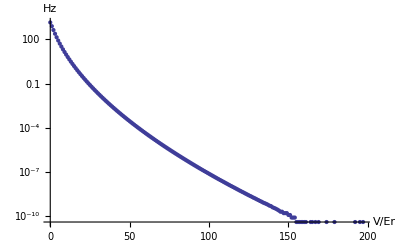

```mathematica
p1 = ListLogPlot[tunplotvsV,AxesLabel->{"V/Er","Hz"}]
```

```mathematica
tunplotvsVZOOM = Table[{V,tunel[V]*Et2/(2*π*ℏ)},{V,0,25,1}];
```

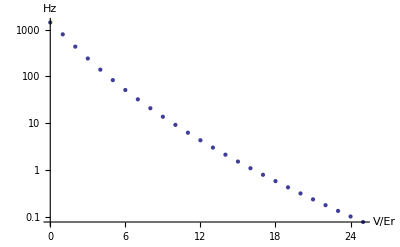

```mathematica
p2 = ListLogPlot[tunplotvsVZOOM,AxesLabel->{"V/Er","Hz"}]
```

```mathematica
(*Check to make sure that I am generating the right stuff. Now, the plot below was created using 727 nm wavelength, and is plotted J/Er, and V/Er. It matches up to the zoller paper*)
```

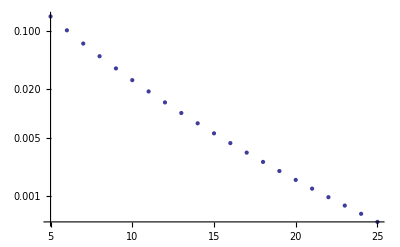

```mathematica
(*The plan is to choose 3 interwell spacing, and show how the tunneling varies as the well depth increases*)

b1 = .9*10^-6
```

9.×10^-7

```mathematica
b1/waist
```

1.2

```mathematica
tunelb1[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et1*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et1*2))])
```

```mathematica
Et1 = π^2*ℏ^2/(2*mRb*(b1/2)^2)
```

1.87798×10^-30

```mathematica
RootApproximant[1.8779841150616613*^-30]
```

1/532485867148650592292051091456

```mathematica
Denominator[1/532485867148650592292051091456]
```

532485867148650592292051091456

```mathematica
tunplotvsVb1 = Table[{V,tunelb1[V]*Et1/(2*π*ℏ)},{V,0,100,1}];
```

```mathematica
(*Now, create my tunneling rates*)
```

```mathematica
tunmeb1 = Table[{V,(computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b1/waist)/2.,12,100][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b1/waist)/2.,12,100][[1]][[1]])*scalin/2},{V,0,100}]
```

{{0,14.1712},{1,242.727},{2,264.476},{3,263.111},{4,253.357},{5,239.999},{6,225.159},{7,209.931},{8,194.918},{9,180.459},{10,166.741},{11,153.861},{12,141.853},{13,130.716},{14,120.426+7.15541×10^-11 ⅈ},{15,110.945},{16,102.227},{17,94.2215},{18,86.8765},{19,80.1418},{20,73.9683},{21,68.3096},{22,63.1223},{23,58.3659},{24,54.003},{25,49.9993},{26,46.3232},{27,42.9461},{28,39.8417},{29,36.9863},{30,34.358-1.93298×10^-9 ⅈ},{31,31.9372},{32,29.7061},{33,27.6482},{34,25.7489},{35,23.9947},{36,22.3735},{37,20.874},{38,19.4864},{39,18.2012},{40,17.0103},{41,15.906},{42,14.8813},{43,13.93},{44,13.0462},{45,12.2246},{46,11.4604},{47,10.7492},{48,10.087},{49,9.47001},{50,8.89487},{51,8.35846},{52,7.85791},{53,7.3906},{54,6.9541},{55,6.5462},{56,6.16485},{57,5.80815},{58,5.47438},{59,5.16193},{60,4.86932},{61,4.59519},{62,4.33826},{63,4.09739},{64,3.87147},{65,3.65953},{66,3.46062},{67,3.2739},{68,3.09857},{69,2.93389},{70,2.77917},{71,2.63379},{72,2.49715},{73,2.3687},{74,2.24793},{75,2.13438},{76,2.02759},{77,1.92715},{78,1.83268},{79,1.74383},{80,1.66026},{81,1.58166},{82,1.50774},{83,1.43823},{84,1.37288},{85,1.31144},{86,1.25371},{87,1.19947},{88,1.14852},{89,1.1007},{90,1.05583},{91,1.01374-3.74395×10^-11 ⅈ},{92,0.9743},{93,0.937361},{94,0.902794},{95,0.870476},{96,0.840293},{97,0.812136},{98,0.785904},{99,0.761503},{100,0.738841}}

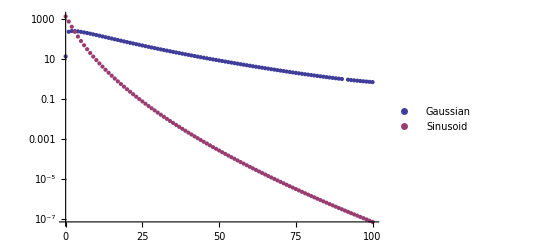

```mathematica
ListLogPlot[{tunmeb1,tunplotvsVb1},PlotLegends->{"Gaussian","Sinusoid"}]
```

```mathematica
Er/(2*π*ℏ)/scalin
```

15.2958

```mathematica
(*Due to the way that Adam's Code is set up, it is a little difficult to create a plot of the tunneling rates. So I will just choose 3 values for the potential, and show that they are equal*)
```

```mathematica
(*Choose V = 5*Er, 25Er, and 100Er*)
```

```mathematica
(*Adam = {239.999, 49.9993, .722277} Hz
```

```mathematica
(computePlaneMatrix2Well[Er/(2*π*ℏ)*5/scalin,.5,(b1/waist)/2.,12,99][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*5/scalin,.5,(b1/waist)/2.,12,99][[1]][[1]])*scalin/2
```

239.999

```mathematica
(computePlaneMatrix2Well[Er/(2*π*ℏ)*25/scalin,.5,(b1/waist)/2.,12,99][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*25/scalin,.5,(b1/waist)/2.,12,99][[1]][[1]])*scalin/2
```

49.9993

```mathematica
(computePlaneMatrix2Well[Er/(2*π*ℏ)*100/scalin,.5,(b1/waist)/2.,12,99][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*100/scalin,.5,(b1/waist)/2.,12,99][[1]][[1]])*scalin/2
```

0.722277

```mathematica
(*So it all works now*)
```

```mathematica
(*NOW look at another b*)
```

```mathematica
b2 = .85*10^-6
```

8.5×10^-7

```mathematica
b2/waist
```

1.13333

```mathematica
Et2 = π^2*ℏ^2/(2*mRb*(b2/2)^2)
```

2.10542×10^-30

```mathematica
tunelb2[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et2*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et2*2))])
```

1.87798×10^-30

```mathematica
tunplotvsVb2 = Table[{V,tunelb2[V]*Et2/(2*π*ℏ)},{V,0,100,1}];
```

```mathematica
tunmeb2 = Table[{V,(computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b2/waist)/2.,12,100][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b2/waist)/2.,12,100][[1]][[1]])*scalin/2},{V,0,100}]
```

```mathematica
(*Also, recreate the figure in JZ paper*)
```

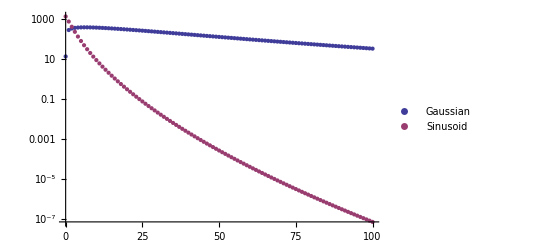

```mathematica
ListLogPlot[{tunmeb2,tunplotvsVb2},PlotLegends->{"Gaussian","Sinusoid"}]
```

```mathematica
(*Now, look at the last b3*)
```

```mathematica
b3 = .75*10^-6
```

7.5×10^-7

```mathematica
b3/waist
```

1.

```mathematica
Et3 = π^2*ℏ^2/(2*mRb*(b3/2)^2)
```

2.7043×10^-30

```mathematica
tunelb3[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et3*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et3*2))])
```

1.87798×10^-30

```mathematica
tunplotvsVb3 = Table[{V,tunelb2[V]*Et3/(2*π*ℏ)},{V,0,100,1}];
```

```mathematica
tunmeb3 = Table[{V,(computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b3/waist)/2.,12,100][[1]][[2]]-computePlaneMatrix2Well[Er/(2*π*ℏ)*V/scalin,.5,(b3/waist)/2.,12,100][[1]][[1]])*scalin/2},{V,0,100}]
```

{{0,14.1712},{1,410.225},{2,547.558},{3,643.335},{4,719.393},{5,783.531},{6,839.542},{7,889.595},{8,935.058},{9,976.857},{10,1015.65},{11,1051.93},{12,1086.06},{13,1118.34},{14,1149.},{15,1178.22},{16,1206.18},{17,1232.98},{18,1258.75},{19,1283.59},{20,1307.56},{21,1330.74},{22,1353.2},{23,1374.99},{24,1396.15},{25,1416.73},{26,1436.77},{27,1456.3},{28,1475.36},{29,1493.96},{30,1512.14},{31,1529.92},{32,1547.32},{33,1564.36},{34,1581.06},{35,1597.44},{36,1613.5},{37,1629.27},{38,1644.76},{39,1659.98},{40,1674.94},{41,1689.65},{42,1704.12},{43,1718.37},{44,1732.4},{45,1746.21},{46,1759.83},{47,1773.24},{48,1786.47},{49,1799.51},{50,1812.38},{51,1825.08},{52,1837.61},{53,1849.98},{54,1862.2},{55,1874.27},{56,1886.19},{57,1897.97},{58,1909.61},{59,1921.12},{60,1932.5},{61,1943.76},{62,1954.89},{63,1965.9},{64,1976.8},{65,1987.58},{66,1998.26},{67,2008.82},{68,2019.29},{69,2029.65},{70,2039.91},{71,2050.07},{72,2060.14},{73,2070.11},{74,2079.99},{75,2089.79},{76,2099.5},{77,2109.12},{78,2118.66},{79,2128.12},{80,2137.5},{81,2146.8},{82,2156.03},{83,2165.18},{84,2174.26},{85,2183.26},{86,2192.2},{87,2201.06},{88,2209.86},{89,2218.59},{90,2227.26},{91,2235.86},{92,2244.4},{93,2252.88},{94,2261.3},{95,2269.66},{96,2277.96},{97,2286.2},{98,2294.38},{99,2302.51},{100,2310.59}}

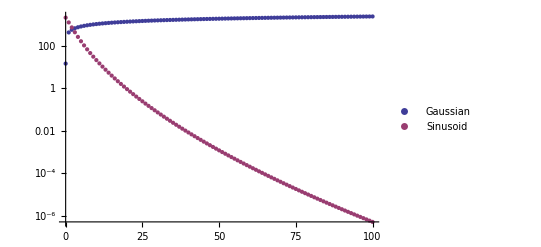

```mathematica
ListLogPlot[{tunmeb3,tunplotvsVb3},PlotLegends->{"Gaussian","Sinusoid"}]
```

### Figure Showing Relation between the two potentials

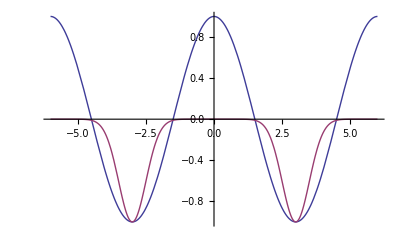

```mathematica
Plot[{Cos[2*π/6*x],-Exp[-2*(x-3)^2]-Exp[-2*(x+3)^2]},{x,-6,6}]
```

```mathematica
(*Try varying the bump height*)
```

```mathematica
Export["gausvsinover.eps",Plot[{-1+Cos[2*π/6*x],-2*Exp[-2*(x-3)^2]-2*Exp[-2*(x+3)^2]},{x,-6,6}]]
```

gausvsinover.eps

```mathematica
(*Try the results with this new congfiguations*)
```

### Bump Height

```mathematica
b4 = 1*10^-6
```

1/1000000

```mathematica
b4/waist
```

1.33333

```mathematica
Et4 = π^2*ℏ^2/(2*mRb*(b4)^2)
```

3.80292×10^-31

```mathematica
tunelb4[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et4*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et4*2))])
```

1.87798×10^-30

```mathematica
tunplotvsVb4 = Table[{V,tunelb4[V]*Et4/(2*π*ℏ)},{V,0,100,5}];
```

```mathematica
tunmeb4=tunelb3
```

tunelb3

```mathematica
tunmeb4 = Table[{V,(computePlaneMatrix2Well[2*Er/(2*π*ℏ)*V/scalin,.5,(b4/waist)/2.,12,300][[1]][[2]]-computePlaneMatrix2Well[2*Er/(2*π*ℏ)*V/scalin,.5,(b4/waist)/2.,12,300][[1]][[1]])*scalin/2},{V,0,100,5}]
```

{{0,14.1712},{5,15.7291},{10,1.94737},{15,0.35077},{20,0.0790298},{25,0.0207399},{30,0.00609101},{35,0.00195245},{40,0.000672509},{45,0.000245251},{50,0.0000942709},{55,0.0000377661},{60,0.0000158743},{65,6.49895×10^-6},{70,2.9847×10^-6},{75,1.5766×10^-6},{80,7.94316×10^-7},{85,2.28667×10^-7+4.90101×10^-9 ⅈ},{90,3.00877×10^-7},{95,1.92562×10^-7-1.92108×10^-10 ⅈ},{100,2.40702×10^-7}}

```mathematica
(computePlaneMatrix2Well[2*Er/(2*π*ℏ)*60/scalin,.5,(b4/waist)/2.,12,300][[1]][[2]]-computePlaneMatrix2Well[2*Er/(2*π*ℏ)*60/scalin,.5,(b4/waist)/2.,12,300][[1]][[1]])*scalin/2
```

0.0000158743

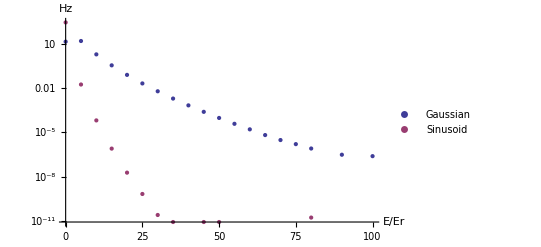

```mathematica
ListLogPlot[{tunmeb4,tunplotvsVb4},PlotLegends->{"Gaussian","Sinusoid"},AxesLabel->{"E/Er","Hz"}]
```

```mathematica
ftunmeb4=Interpolation[tunmeb4,InterpolationOrder->0]
```

InterpolatingFunction[{{0.,100.}},<>]

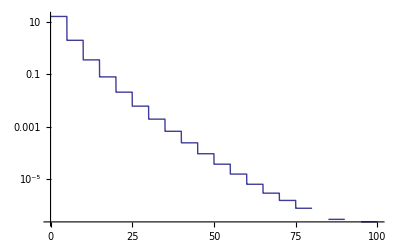

```mathematica
LogPlot[ftunmeb4[x],{x,0,100}]
```

```mathematica
fplotVb4=Interpolation[tunplotvsVb4,InterpolationOrder->0]
```

InterpolatingFunction[{{0.,100.}},<>]

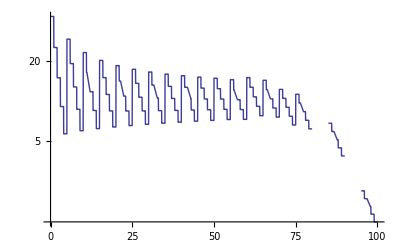

```mathematica
LogPlot[fplotVb4[x]/ftunmeb4[x],{x,0,100}]
```

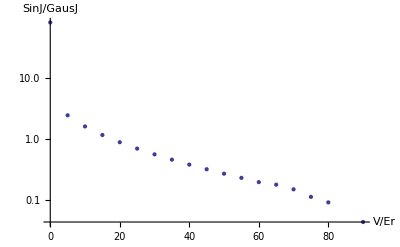

```mathematica
ListLogPlot[Table[{tunmeb4[[p,1]],tunplotvsVb4[[p,2]]/tunmeb4[[p,2]]},{p,1,20}],AxesLabel->{"V/Er","SinJ/GausJ"}]
```

### Bump Height 2

```mathematica
b5 = .9*10^-6
```

9.×10^-7

```mathematica
b5/waist
```

1.2

```mathematica
Et5= π^2*ℏ^2/(2*mRb*(b5/2)^2)
```

1.87798×10^-30

```mathematica
tunelb5[V_]:=1/2(MathieuCharacteristicA[.999,(V*Er*1/(Et5*2))]-MathieuCharacteristicA[0,(V*Er*1/(Et5*2))])
```

1.87798×10^-30

```mathematica
tunplotvsVb5 = Table[{V,tunelb5[V]*Et5/(2*π*ℏ)},{V,0,100,5}];
```

tunelb3

```mathematica
tunmeb5= Table[{V,(computePlaneMatrix2Well[2*Er/(2*π*ℏ)*V/scalin,.5,(b5/waist)/2.,12,300][[1]][[2]]-computePlaneMatrix2Well[2*Er/(2*π*ℏ)*V/scalin,.5,(b5/waist)/2.,12,300][[1]][[1]])*scalin/2},{V,0,100,5}]
```

{{0,14.1712},{5,166.741},{10,73.9683},{15,34.3579},{20,17.0096},{25,8.89147},{30,4.85884},{35,2.75405},{40,1.60959},{45,0.96559},{50,0.592474},{55,0.370788},{60,0.236141},{65,0.152757},{70,0.100215},{75,0.0665888},{80,0.0447628},{85,0.0304131},{90,0.0208677},{95,0.014449},{100,0.0100893}}

```mathematica
(computePlaneMatrix2Well[2*Er/(2*π*ℏ)*60/scalin,.5,(b5/waist)/2.,12,300][[1]][[2]]-computePlaneMatrix2Well[2*Er/(2*π*ℏ)*60/scalin,.5,(b5/waist)/2.,12,300][[1]][[1]])*scalin/2
```

0.236141

```mathematica
tunmeb5={{0,14.171200342784388},{5,15.72909872548134},{10,1.9473698793341594},{15,0.35077046948553525},{20,0.0790297768666891},{25,0.020739947270634287},{30,0.006091009850035075},{35,0.0019524535035707884},{40,0.0006725090878754366},{45,0.00024525117115062274},{50,0.0000942709011494174},{55,0.00003776612891700138},{60,0.000015874290644208036},{65,6.498951438872131*^-6},{70,2.9847036237783116*^-6},{75,1.5765974786893502*^-6},{80,7.943162869732604*^-7},{85,2.2866680988624161*^-7+4.9010104709376415*^-9 ⅈ},{90,3.008773814292653*^-7},{95,1.9256152411472979*^-7-1.921083942994114*^-10 ⅈ},{100,2.407019051434122*^-7}}
```

{{0,14.1712},{5,15.7291},{10,1.94737},{15,0.35077},{20,0.0790298},{25,0.0207399},{30,0.00609101},{35,0.00195245},{40,0.000672509},{45,0.000245251},{50,0.0000942709},{55,0.0000377661},{60,0.0000158743},{65,6.49895×10^-6},{70,2.9847×10^-6},{75,1.5766×10^-6},{80,7.94316×10^-7},{85,2.28667×10^-7+4.90101×10^-9 ⅈ},{90,3.00877×10^-7},{95,1.92562×10^-7-1.92108×10^-10 ⅈ},{100,2.40702×10^-7}}

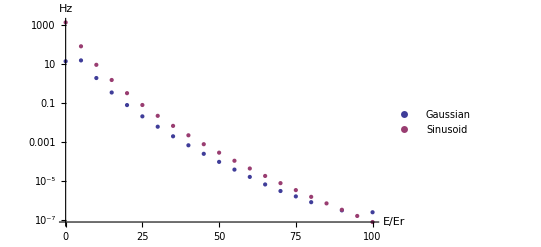

```mathematica
ListLogPlot[{tunmeb5,tunplotvsVb5},PlotLegends->{"Gaussian","Sinusoid"},AxesLabel->{"E/Er","Hz"}]
```

```mathematica
ftunmeb4=Interpolation[tunmeb4,InterpolationOrder->0]
```

InterpolatingFunction[{{0.,100.}},<>]

```mathematica
LogPlot[ftunmeb4[x],{x,0,100}]
```

-Graphics-

```mathematica
fplotVb4=Interpolation[tunplotvsVb4,InterpolationOrder->0]
```

InterpolatingFunction[{{0.,100.}},<>]

```mathematica
LogPlot[fplotVb4[x]/ftunmeb4[x],{x,0,100}]
```

-Graphics-

```mathematica
Export["errorgausvsin.eps",ListPlot[Table[{tunmeb5[[p,1]],tunplotvsVb5[[p,2]]/tunmeb4[[p,2]]},{p,1,20}],AxesLabel->{"V/Er","SinJ/GausJ"}]]
```

errorgausvsin.eps

## Functions:

```mathematica
Clear[h]
Clear[M]
h = 1.05457173*10^-34;
M = 1.443161*10^-25;
```

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Compile[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

0.0103913

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Compile[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

(1-size)/2+(i-Mod[i,size,1])/size

```mathematica
kx[6,5]
```

-1

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2WellH[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]

]
```

```mathematica
computePlaneMatrix2WellBox[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - 1/2(V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[1/(2 c^2)(-b+ⅈ*c^2(m-l))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length)-1/2(V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[(1/(2 c^2)(b+ⅈ*c^2(m-l))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length);
M = Eigensystem[Table[H[π*l/length,π*m/length],{l,1,p},{m,1,p}]-10000*IdentityMatrix[p],3]

]
```

```mathematica
ComputePlaneWaveEN[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigenvalues[M-10000*IdentityMatrix[p^2],3]
]
```

```mathematica
(-bsep+ⅈ*c^2(l-m))^2//Expand
```

bsep^2-2 ⅈ bsep c^2 l-c^4 l^2+2 ⅈ bsep c^2 m+2 c^4 l m-c^4 m^2

```mathematica
1/2 (k-l) (2 ⅈ bsep+(-k+l) w^2)//Expand
```

ⅈ bsep k-ⅈ bsep l-(k^2 w^2)/2+k l w^2-(l^2 w^2)/2

```mathematica
Tunneling2D[V_,L_,p_,b_]:= Module[{En0,En1, EnList,T},
EnList = Eigenvalues[BuildPlaneMatrix2D2Well[V,L,p,b/2.]-1000.*IdentityMatrix[p^2],2]+1000;
En1 = EnList[[2]];
En0  =EnList [[1]];
T = En1-En0
]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2*c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```